# Mały Projekt 6 - Grafy

## Jan Czechowski

## zadanie 1.

-Graphics-

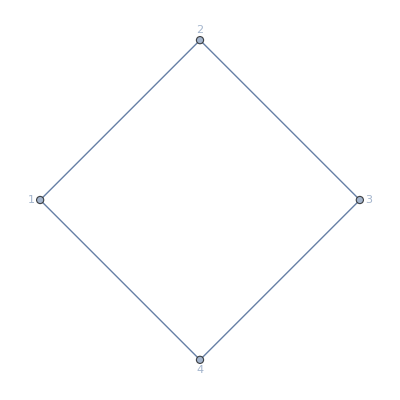

```mathematica
GraphPlot[CycleGraph[4],VertexLabels->"Name"]
```

## zadanie 2.

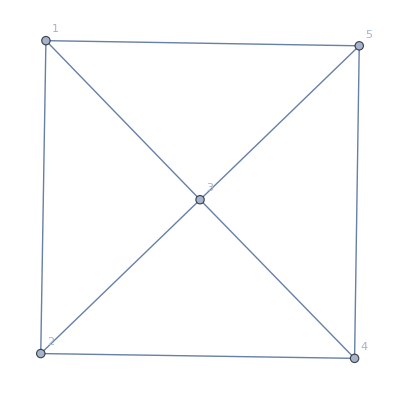

```mathematica
GraphPlot[Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->3,2<->4,3<->5}],VertexLabels->"Name"]
```

## zadanie 3.

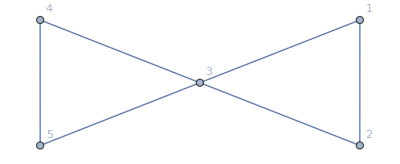

{{{1<->3,3<->5,5<->4,4<->3,3<->2,2<->1}},{}}

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->5,5<->3,3<->1},VertexLabels->"Name"]
{FindEulerianCycle[g],FindHamiltonianCycle[g]}
```

## zadanie 4.

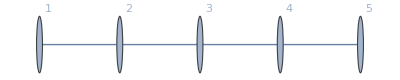

```mathematica
GraphPlot[Graph[{1<->2,2<->3,3<->4,4<->5}],VertexLabels->"Name"]
```

## zadanie 5.

```mathematica
GenerateGrayCode[1]:={{0},{1}}
GenerateGrayCode[n_Integer]:=Module[{prev,with0,with1},prev=GenerateGrayCode[n-1];
with0=Prepend[#,0]&/@prev;
with1=Prepend[#,1]&/@Reverse[prev];
Join[with0,with1]]

TableForm[Table[{"n = "<>ToString[n],Reverse[GenerateGrayCode[n]]},{n,2,5}]]
```

n = 2 | 1 | 0
1 | 1
0 | 1
0 | 0
n = 3 | 1 | 0 | 0
1 | 0 | 1
1 | 1 | 1
1 | 1 | 0
0 | 1 | 0
0 | 1 | 1
0 | 0 | 1
0 | 0 | 0
n = 4 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 1 | 0
1 | 1 | 1 | 0
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 0 | 0
0 | 1 | 0 | 0
0 | 1 | 0 | 1
0 | 1 | 1 | 1
0 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0
n = 5 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0

## zadanie 6.

```mathematica
grafGraya[n_]:=Graph[Range[0,2^n-1],Flatten[Table[UndirectedEdge[i,j],{i,0,2^n-1},{j,i+1,2^n-1}],1],VertexLabels->"Name"]
```

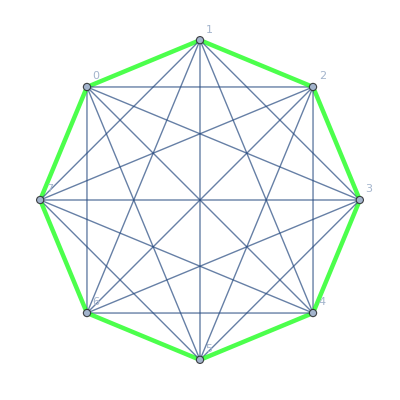

```mathematica
cykl8=FindHamiltonianCycle[grafGraya[3]];
HighlightGraph[grafGraya[3],Style[cykl8,Thickness[0.008],Green]]
```

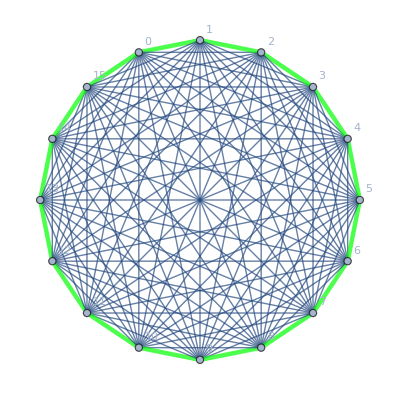

```mathematica
cykl16=FindHamiltonianCycle[grafGraya[4]];
HighlightGraph[grafGraya[4],Style[cykl16,Thickness[0.008],Green]]
```

## zadanie 7.

```mathematica
tree=TreeGraph[{1->2,1->3,2->4,2->5}];
```

```mathematica
pruferCode=ResourceFunction["LabeledTreeToPruferCode"][tree]
```

{1,2,2}

```mathematica
TreeGraph[{1->2,1->3,2->4,2->5},VertexLabels->"Name",GraphStyle->"NameLabeled"]
```

-Graphics-

## zadanie 8.

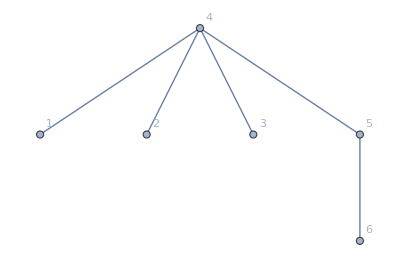

```mathematica
TreeFromPrufer[pruferCode_List]:=Module[{n,vertices,degrees,edges={},pruferSequence=pruferCode},n=Length[pruferCode]+2;vertices=Range[n];degrees=Table[1,{n}];
Do[degrees[[v]]++,{v,pruferSequence}];
While[Length[pruferSequence]>0,v=First[Select[vertices,degrees[[#]]==1&]];
AppendTo[edges,UndirectedEdge[v,First[pruferSequence]]];
degrees[[v]]--;
degrees[[First[pruferSequence]]]--;
pruferSequence=Rest[pruferSequence];];
AppendTo[edges,UndirectedEdge@@Select[vertices,degrees[[#]]==1&]];
Graph[vertices,edges,VertexLabels->"Name"]];

pruferCode={4,4,4,5};
tree=TreeFromPrufer[pruferCode]
```

## zadanie 9.

```mathematica
W="aaaaaabbbbabbccccccaaaaccbbaddaadddddaaaaabbbdddddbcccaaaaaaddddddddbbbb";
czestotliwosci=Tally[Characters[W]]
```

{{a,25},{b,16},{c,11},{d,20}}

```mathematica
zamiana=<|"a"->"11","b"->"01","c"->"00","d"->"10"|>;

zakodowanaWiadomosc=StringJoin[Riffle[zamiana[#]&/@Characters[W]," "]]
```

11 11 11 11 11 11 01 01 01 01 11 01 01 00 00 00 00 00 00 11 11 11 11 00 00 01 01 11 10 10 11 11 10 10 10 10 10 11 11 11 11 11 01 01 01 10 10 10 10 10 01 00 00 00 11 11 11 11 11 11 10 10 10 10 10 10 10 10 01 01 01 01

## zadanie 10.

Należy pytać tak jak według schematu poniżej aby średnia liczba pytań była najmniejsza. Ten schemat pozwoli ustalić imię losowo poznanej kobiety w 2 lub 3 pytaniach.

Pierwsze pytanie: ”Czy to Anna lub Barbara?”

TAK→Przechodzimy do pytania 2A.
NIE→Przechodzimy do pytania 2B

Drugie pytanie (2A):”Czy to Anna?”

TAK→To Anna (35%).
NIE→To Barbara (34%).

Lub

Drugie pytanie (2B):”Czy to Cecylia?”

TAK→To Cecylia (16%).
NIE→Przechodzimy do pytania 3.

Trzecie pytanie:”Czy to Dorota?”

TAK→To Dorota (8%).
NIE→To Elżbieta (7%).